# Drugi kviz

Vsaka podnaloga je vredna 1 točko, razen če je pri podnalogi zapisano drugače. Skupno je moč doseči 20 točk.

## Naloga 1

a)  Definirajte funkcijo , ki sprejme naravni števili  in  in vrne matriko dimenzije , kjer se na vsakem mestu v matriki pojavi produkt indeksa stolpca in indeksa vrstice (začnemo šteti z 1).

```mathematica
A[n_,m_]:=Table[x*y, {x,1,n},{y,1,m}]
```

```mathematica
A[3,3]//MatrixForm
```

(1 | 2 | 3
2 | 4 | 6
3 | 6 | 9)

b) Pokažite, da je  simetrična matrika.

```mathematica
A[3,3]==Transpose[A[3,3]]
```

True

c) Izračunajte lastne vrednosti in lastne vektorje matrike .

```mathematica
{lastneVrednosti,lastniVektorji} = Eigensystem[A[10,10]];
```

d) Izračunajte karakteristični polinom matrike .

```mathematica
karakterističniPol = Det[A[10,10]-x*IdentityMatrix[10]]
```

-385 x^9+x^10

e) Matriko  diagonalizirajte. Določite ustrezno diagonalno matriko , prehodno matriko  in .

```mathematica
G = DiagonalMatrix[lastneVrednosti]
```

{{385,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
P = Transpose[lastniVektorji]
```

{{1,-10,-9,-8,-7,-6,-5,-4,-3,-2},{2,0,0,0,0,0,0,0,0,1},{3,0,0,0,0,0,0,0,1,0},{4,0,0,0,0,0,0,1,0,0},{5,0,0,0,0,0,1,0,0,0},{6,0,0,0,0,1,0,0,0,0},{7,0,0,0,1,0,0,0,0,0},{8,0,0,1,0,0,0,0,0,0},{9,0,1,0,0,0,0,0,0,0},{10,1,0,0,0,0,0,0,0,0}}

f) (2 točki) Rešite matrično enačbo .

```mathematica
LinearSolve[(A[10,10]+P-G),IdentityMatrix[10]]
```

{{-53/20251,664/20251,534/20251,404/20251,274/20251,144/20251,2/2893,-116/20251,-246/20251,-376/20251},{4/20251,-7692/20251,-6918/20251,-6144/20251,-5370/20251,-4596/20251,-546/2893,-3048/20251,-2274/20251,18751/20251},{18/101255,-34614/101255,-31131/101255,-27648/101255,-4833/20251,-20682/101255,-2457/14465,-13716/101255,91022/101255,-1350/20251},{16/101255,-30768/101255,-27672/101255,-24576/101255,-4296/20251,-18384/101255,-2184/14465,89063/101255,-9096/101255,-1200/20251},{2/14465,-3846/14465,-3459/14465,-3072/14465,-537/2893,-2298/14465,12554/14465,-1524/14465,-1137/14465,-150/2893},{12/101255,-23076/101255,-20754/101255,-18432/101255,-3222/20251,87467/101255,-1638/14465,-9144/101255,-6822/101255,-900/20251},{2/20251,-3846/20251,-3459/20251,-3072/20251,17566/20251,-2298/20251,-273/2893,-1524/20251,-1137/20251,-750/20251},{8/101255,-15384/101255,-13836/101255,88967/101255,-2148/20251,-9192/101255,-1092/14465,-6096/101255,-4548/101255,-600/20251},{6/101255,-11538/101255,90878/101255,-9216/101255,-1611/20251,-6894/101255,-819/14465,-4572/101255,-3411/101255,-450/20251},{4/101255,93563/101255,-6918/101255,-6144/101255,-1074/20251,-4596/101255,-546/14465,-3048/101255,-2274/101255,-300/20251}}

g) Ali je matrika  obrnljiva?

```mathematica
A[10,10]==Inverse[P]*A[10,10]*P
```

False

## Naloga 2

Imamo klančino z naklonom 20 stopinj dolžine 5m. Na dnu klančine se nahaja ravnina dolžine 10m.
Kroglico z radijem 20cm potisnemo s skrajno desnega roba ravnine s hitrostjo v0 = 11m/s. Ko pride kroglica na vrh klančine, skoči čez rob, dokler ne pristane na tleh (poševni met). 
Predpostavite lahko, da med kroglico in podlago ni trenja in da se zaradi kotaljenja energija ne izgublja. Simulirajte gibanje kroglice do trenutka ko pristane na tleh.
Za gravitacijski pospešek vzemite g = 9.81 m/s^2, za simulacijo pa vzemite  . (Glej sliko).

```mathematica
naklon = 20;
dolzinaKlanca = 50;
dolzinaRavnine = 100;
radijKrogle = 2;
```

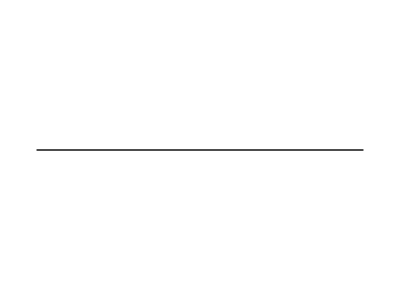

```mathematica
ravnina = Graphics[{
Line[{{0,0},{dolzinaRavnine,0}}]
}]
```

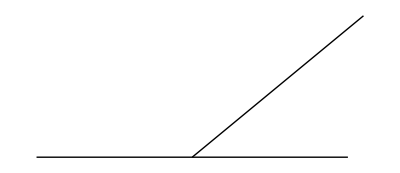

```mathematica
klanec = Graphics[{
Line[{{dolzinaRavnine/2,0},{dolzinaRavnine+dolzinaKlanca,dolzinaKlanca*Sin[naklon]}}],
Line[{{0,0},{dolzinaRavnine,0}}]
}]
```

```mathematica
Graphics[{klanec,ravnina}]
```

-Graphics-

a) Definiraj gravitacijski pospešek, naklon, dolžino klanca, dolžino podlage, začetno hitrost in radij kroglice.

b) Nariši klančino in tla.

c) Na sliko dodaj kroglico tako, da se bo kroglica premaknila, če se spremeni njeno središče (Uporabi `Dynamic`).

d) Definiraj funkcijo `naKlancu`, ki sprejme središče kroglice in vrne `True`, če je kroglica na klancu.

e) Definiraj funkcijo `posodobiHitrost`, ki sprejme vektor trenutne hitrost kroglice in kot α ter vrne novo hitrost, gibanja po klančini z naklonom α po času Δt.

f) Definiraj funkcijo `hitrostNaKlanec`, ki sprejme vektor trenutne hitrosti kroglice in kot α ter vrne novo hitrost, ki jo dobi kroglica, ko iz ravnega dela preide na klanec z naklonom α.

g) Definiraj funkcijo `posodobiHitrostPosevniMet`, ki sprejme trenutno hitrost kroglice in vrne novo hitrost kroglice po času Δt.

h) Definiraj funkcijo `posodobiLego`, ki sprejme trenutno lego kroglice in njeno hitrost in vrne novo lego kroglice po času Δt.

i) S pomočjo prejšnjih funkcij simuliraj premikanje kroglice. (4 točke - gibanje po ravnini (1 točka), gibanje po klančini (1 točka), gibanje pri poševnem metu (1 točka), simulacija se ustavi, ko žogica pristane na tleh (1 točka))